13.0284

3.12154

0.887111

0.000450231

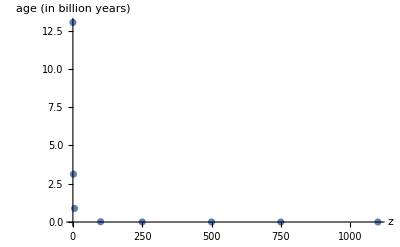

```mathematica
(* (i) Flat Lambda Cold Dark Matter model *)
Subscript[Ω, m]=0.3;
Subscript[Ω, r]=0;
Subscript[Ω, Λ]=0.7;
H[z_]:=0.074 √(Subscript[Ω, m](1+z)^3+Subscript[Ω, r](1+z)^4+Subscript[Ω, Λ]);
NIntegrate[1/H[z] 1/(1+z),{z,0,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,2,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,6,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,1100,Infinity}]
ListPlot[{{0,NIntegrate[1/H[z] 1/(1+z),{z,0,Infinity}]},
{2,NIntegrate[1/H[z] 1/(1+z),{z,2,Infinity}]},
{6,NIntegrate[1/H[z] 1/(1+z),{z,6,Infinity}]},
{100,NIntegrate[1/H[z] 1/(1+z),{z,100,Infinity}]},
{250,NIntegrate[1/H[z] 1/(1+z),{z,250,Infinity}]},
{500,NIntegrate[1/H[z] 1/(1+z),{z,500,Infinity}]},
{750,NIntegrate[1/H[z] 1/(1+z),{z,750,Infinity}]},
{1100,NIntegrate[1/H[z] 1/(1+z),{z,1100,Infinity}]}},AxesLabel->{"z","age (in billion years)"},PlotRange->Full]
```

12.3049

3.02706

0.880994

0.000450231

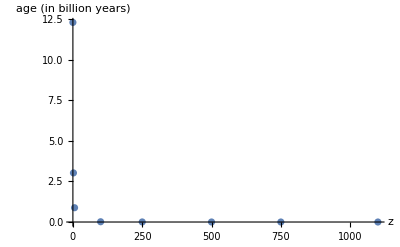

```mathematica
(* (ii) Flat dark energy (with an equation of state Subscript[w, DE]=−0.7 *)
Subscript[Ω, m]=0.3;
Subscript[Ω, r]=0;
Subscript[Ω, Λ]=0.7;
H[z_]:=0.074 √(Subscript[Ω, m](1+z)^3+Subscript[Ω, r](1+z)^4+Subscript[Ω, Λ](1+z)^0.9);
NIntegrate[1/H[z] 1/(1+z),{z,0,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,2,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,6,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,1100,Infinity}]
ListPlot[{{0,NIntegrate[1/H[z] 1/(1+z),{z,0,Infinity}]},
{2,NIntegrate[1/H[z] 1/(1+z),{z,2,Infinity}]},
{6,NIntegrate[1/H[z] 1/(1+z),{z,6,Infinity}]},
{100,NIntegrate[1/H[z] 1/(1+z),{z,100,Infinity}]},
{250,NIntegrate[1/H[z] 1/(1+z),{z,250,Infinity}]},
{500,NIntegrate[1/H[z] 1/(1+z),{z,500,Infinity}]},
{750,NIntegrate[1/H[z] 1/(1+z),{z,750,Infinity}]},
{1100,NIntegrate[1/H[z] 1/(1+z),{z,1100,Infinity}]}},AxesLabel->{"z","age (in billion years)"},PlotRange->Full]
```

13.3886

3.14503

0.887839

0.000450231

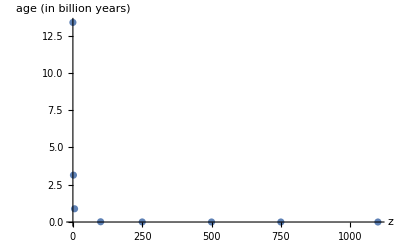

```mathematica
(* (iii) Flat dark energy (with an equation of state Subscript[w, DE]=−1.2 *)
Subscript[Ω, m]=0.3;
Subscript[Ω, r]=0;
Subscript[Ω, Λ]=0.7;
H[z_]:=0.074 √(Subscript[Ω, m](1+z)^3+Subscript[Ω, r](1+z)^4+Subscript[Ω, Λ](1+z)^-0.6);
NIntegrate[1/H[z] 1/(1+z),{z,0,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,2,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,6,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,1100,Infinity}]
ListPlot[{{0,NIntegrate[1/H[z] 1/(1+z),{z,0,Infinity}]},
{2,NIntegrate[1/H[z] 1/(1+z),{z,2,Infinity}]},
{6,NIntegrate[1/H[z] 1/(1+z),{z,6,Infinity}]},
{100,NIntegrate[1/H[z] 1/(1+z),{z,100,Infinity}]},
{250,NIntegrate[1/H[z] 1/(1+z),{z,250,Infinity}]},
{500,NIntegrate[1/H[z] 1/(1+z),{z,500,Infinity}]},
{750,NIntegrate[1/H[z] 1/(1+z),{z,750,Infinity}]},
{1100,NIntegrate[1/H[z] 1/(1+z),{z,1100,Infinity}]}},AxesLabel->{"z","age (in billion years)"},PlotRange->Full]
```

9.6939

1.93545

0.543791

0.000275709

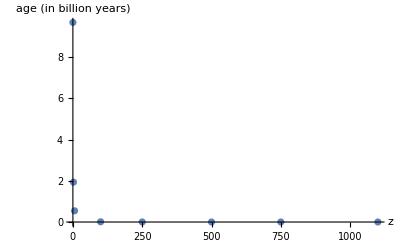

```mathematica
(* (iv) Flat Lambda Cold Dark Matter model with Subscript[Ω, m]=0.8 *)
Subscript[Ω, m]=0.8;
Subscript[Ω, r]=0;
Subscript[Ω, Λ]=0.2;
H[z_]:=0.074 √(Subscript[Ω, m](1+z)^3+Subscript[Ω, r](1+z)^4+Subscript[Ω, Λ]);
NIntegrate[1/H[z] 1/(1+z),{z,0,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,2,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,6,Infinity}]
NIntegrate[1/H[z] 1/(1+z),{z,1100,Infinity}]
ListPlot[{{0,NIntegrate[1/H[z] 1/(1+z),{z,0,Infinity}]},
{2,NIntegrate[1/H[z] 1/(1+z),{z,2,Infinity}]},
{6,NIntegrate[1/H[z] 1/(1+z),{z,6,Infinity}]},
{100,NIntegrate[1/H[z] 1/(1+z),{z,100,Infinity}]},
{250,NIntegrate[1/H[z] 1/(1+z),{z,250,Infinity}]},
{500,NIntegrate[1/H[z] 1/(1+z),{z,500,Infinity}]},
{750,NIntegrate[1/H[z] 1/(1+z),{z,750,Infinity}]},
{1100,NIntegrate[1/H[z] 1/(1+z),{z,1100,Infinity}]}},AxesLabel->{"z","age (in billion years)"},PlotRange->Full]
```